# K-Complexity for Ising Model

## Finding Lanczos Coefficients

### Lanczos Algorithm

```mathematica
MyInnerProd[A_,B_] := Module[{psi},psi = Tr[ConjugateTranspose[A].B]]
```

```mathematica
comm[Op1_,Op2_]:= Module[{com},com= Op1.Op2 - Op2.Op1]
```

```mathematica
(*Calculates with full precision, and only extracts the bn's numerically. VERY SLOW!! *)
Lanczos[H_,S_,nmax_,prec_,btol_] := Module[{b,Op,B,LOp ,NormSq, count},
(*The first iteration is done outside loop to avoid divide by zero errors*)
count=0;
Op[0]=ConstantArray[0,Dimensions[S]];
NormSq[0]=MyInnerProd[Op[0],Op[0]];
Op[1] =  S;
NormSq[1]=MyInnerProd[Op[1],Op[1]];
LOp[1]=comm[H,Op[1]];
B[1]=MyInnerProd[Op[0],LOp[1]];
b[1] = 0;
Op[2]=LOp[1];

Do[LOp[i]=comm[H,Op[i]];
NormSq[i]=MyInnerProd[Op[i],Op[i]];
B[i]=MyInnerProd[Op[i-1],LOp[i]];
Op[i+1] = LOp[i] - B[i]/NormSq[i-1]*Op[i-1];
(*If[Mod[i,15]==0,Op[i]=N[Op[i],20]]; (*New bit in a fruitless attempt to add efficiency*)
If[Mod[i,15]==1,Rationalize[Op[i+1]];
Rationalize[Op[i]];
Rationalize[Norm[i]];
Rationalize[B[i]]; 
Rationalize[LOp[i]]];*)

If[Abs[B[i]]<btol,Print["Cut-off reached at n= ",i,", since B_n and btol are ",B[i]," and ",btol]; (*Break when the Lanczos coefficients reach close to zero*)
Break[]];
b[i]=N[B[i]/Sqrt[NormSq[i]*NormSq[i-1]],prec];
count++
,{i,2,nmax}];
Table[b[i],{i,1,count}]]
```

```mathematica
(*Uses the old technique with numerical float valued matrices which causes massive loss of precision*)
LanczosNum[H_,S_,nmax_,prec_,btol_] := Module[{b,Op,U,LOp, counter,tolval}, 
counter =1;
b[1] = 0;
Op[0]=ConstantArray[0,Dimensions[S]];
Op[1] = (Sqrt[MyInnerProd[S,S]])^(-1) * S;
U[1] = comm[H,Op[1]];

Do[LOp[i]=comm[H,Op[i-1]];
U[i] = LOp[i] - b[i-1]*Op[i-2];
b[i] = Sqrt[MyInnerProd[U[i],U[i]]];
tolval[i]=b[i]/Sqrt[MyInnerProd[LOp[i],LOp[i]]];
(*Print[b[i]," and ",tolval[i]];*)
If[tolval[i]<btol,Print["Cut-off reached at n= ",i,", since tolval(b/(Norm[H, O]))) and btol are ",b[i]," and ",btol];
Break[]];
Op[i] =N[b[i]^(-1), prec] * U[i];
counter++
,{i,2,nmax}];

Table[b[i],{i,1,counter-1}]]
```

### Toda Chain

We can use the Toda hierarchy technique to find the Lanczos coefficients, a_n  and b_n , directly from the auto-correlation function, C. The resulting analytic expressions for a_n  and b_n need to be evaluated at the Euclidean time cut-off that was used to regulate UV divergences in the calculation of C .

```mathematica
(*Input auto correlation function, output a_n's and b_n's, where all are a function of Euclidean time*)
SolveTodaChain[Cψ_, nmax_]:=
Module[{T,b,a},(*Solve for the Toda tau function as a function of Euclidean time*)
T[1]=1;
T[2]=Cψ;
Do[T[n+1]= (T[n]*D[T[n],{t,2}]-D[T[n],t])/T[n-1];
(*Get the a_n's and b_n's from the tau function*)
b[n]=(T[n-1]*T[n+1])/T[n]^2;
a[n]=D[Log[T[n]/T[n-1]],t];
,{n,2,nmax}];
{Table[a[n],{n,2,nmax}], Table[b[n],{n,2,nmax}]}]
```

```mathematica
SolveTodaChain[t^2,4]
```

{{2/t,(t^2 ((-2+4 t)/t^2-(2 (-2 t+2 t^2))/t^3))/(-2 t+2 t^2),(t^2 (-2 t+2 t^2) ((-4+4 (-2+4 t))/(t^2 (-2 t+2 t^2))-((-2+4 t) (2-4 t+4 (-2 t+2 t^2)))/(t^2 (-2 t+2 t^2)^2)-(2 (2-4 t+4 (-2 t+2 t^2)))/(t^3 (-2 t+2 t^2))))/(2-4 t+4 (-2 t+2 t^2))},{(-2 t+2 t^2)/t^4,(2-4 t+4 (-2 t+2 t^2))/((-2 t+2 t^2)^2),(t^4 (-(-4+4 (-2+4 t))/t^2+(2 (2-4 t+4 (-2 t+2 t^2)))/t^3+((2-4 t+4 (-2 t+2 t^2)) (16/t^2-(4 (-4+4 (-2+4 t)))/t^3+(6 (2-4 t+4 (-2 t+2 t^2)))/t^4))/t^2))/((2-4 t+4 (-2 t+2 t^2))^2)}}

## Generating Spin Matrices

We need to convert our Spin operators into matrices. The matrices are made by taking Kronecker product along the chain of the operator at each site.

```mathematica
(*For Ising Matrix. Given a binary number occupation rep of spins, it gives the corresponding matrix*)
SpinStateMatrix[OccRep_, Spin_] := Module[{a}, 
a=IdentityMatrix[1];
Do[ If[OccRep[[i]]==0, a = KroneckerProduct[a,IdentityMatrix[Dimensions[Spin]]]];
If[OccRep[[i]]==1, a = KroneckerProduct[a, Spin]];
,{i, 1, Length[OccRep]}];
a]
```

```mathematica
(*For Ising Matrix. Given Length, Interaction Spins, Number of Interaction Spins (k-local), And the Spins for 2 magnetic fields, it Generates the Matrix representation.*)
IsingSum[L_,IntSpin_,IntSpinNo_,BSpin1_,BSpin2_]:=Module[{IntPerms, IntPieces, IntPart, B1Part, B2Part, SingleSpinPerms, B1Pieces, B2Pieces},
IntPerms = Table[Join[ConstantArray[0,i-1],ConstantArray[1,IntSpinNo],ConstantArray[0,L-(i-1)-IntSpinNo]],{i,1,L-IntSpinNo+1}];
SingleSpinPerms=Table[Join[ConstantArray[0,i-1],ConstantArray[1,1],ConstantArray[0,L-(i-1)-1]],{i,1,L}];
If[IntSpin == 0, IntPart = IntSpin, IntPart =IntSpin,
IntPieces = Table[SpinStateMatrix[IntPerms[[i]], IntSpin],{i, 1, Length[IntPerms]}];
IntPart = Total[IntPieces]];
If[BSpin1 == 0, B1Part=BSpin1,B1Part=BSpin1,
B1Pieces=Table[SpinStateMatrix[SingleSpinPerms[[i]],BSpin1],{i,1,Length[SingleSpinPerms]}];
B1Part = Total[B1Pieces]];
If[BSpin2 == 0, B2Part = BSpin2,B2Part=BSpin2,
B2Pieces =Table[SpinStateMatrix[SingleSpinPerms[[j]],BSpin2],{j,1,Length[SingleSpinPerms]}];
B2Part = Total[B2Pieces]];
IntPart+B1Part+B2Part]
```

## K-Complexity

In order to extract the Krylov Complexity from the Lanczos coefficients we can solve the 1D particle hopping equation for phi
	∂_t ϕ  = ϕ_(n-1)b_n - b_(n-1)ϕ_(n+1)  
But the phi index starts from 0 and the b index starts from 1. So,  b_n->b_n+1 to match up the b’s with phi’s correctly. 
We also prepend and append 0 to the Lanczos coefficients. So thus b_1=0 and b_(m+2)=0.
    i.e.	  	∂_t ϕ_0  = b_1 ϕ_-1 - b_2 ϕ_1 ,    			 (but the first term vanishes since b_1=0) 
    	 	∂_t ϕ_1  = b_2 ϕ_0 - b_3 ϕ_2  ,
    	 	...
    	 	∂_t ϕ_n  = b_(n+1) ϕ_(n-1)- b_(n+2)ϕ_(n+1)  
    	 	...
    	 	∂_m ϕ_1  = b_(m+1)ϕ_(m-1) - b_(m+2)ϕ_(m+1)	(but the last term vanishes since b_(m+2)=0)
And now we can solve for ϕ_0 to ϕ_m.
And then use phi to find the Krylov-complexity and the normalized Krylov Complexity
	K(t)=∑_n n ϕ_n^*ϕ_n
K_norm(t)=(∑_n n ϕ_n^*ϕ_n)/(∑_n ϕ_n^*ϕ_n)

```mathematica
KComplexityFromBs[b_,bmax_,tmax_]:=Module[{ϕ,soln,bNew, bSlice,f,K,NormK},
(*Solve the particle hopping equation with Zero BC on n, and IC of Subscript[ϕ, n](0)= Subscript[δ, n](0)*)

bSlice=b[[;;bmax+1]];
bNew= Append[bSlice,0];
soln=NDSolve[Join[Table[D[ϕ[n,t],t]==
 bNew[[n+1]]*ϕ[n-1,t]- bNew[[n+2]]*ϕ[n+1,t],{n,0,bmax}],
Table[ϕ[n,0]==KroneckerDelta[n,0],{n,0,bmax}]],{Table[ϕ[n,t],{n,0,bmax}]},{t,0,tmax}];
(*Extract the phi's from the solution*)
f=soln[[1]][[1]][[2]];
(*Calculate the K-Complexity from the phi's*)
K = Sum[n*Conjugate[f[[n+1]]]*f[[n+1]],{n,1, bmax}]
]
```

```mathematica
NormKComplexityFromBs[b_,bmax_,tmax_]:=Module[{ϕ,soln,bNew, bSlice,f,K,NormK},
(*Solve the particle hopping equation with Zero BC on n, and IC of Subscript[ϕ, n](0)= Subscript[δ, n](0)*)

bSlice=b[[;;bmax+1]];
bNew= Append[bSlice,0];
soln=NDSolve[Join[Table[D[ϕ[n,t],t]==
 bNew[[n+1]]*ϕ[n-1,t]- bNew[[n+2]]*ϕ[n+1,t],{n,0,bmax}],
Table[ϕ[n,0]==KroneckerDelta[n,0],{n,0,bmax}]],{Table[ϕ[n,t],{n,0,bmax}]},{t,0,tmax}];
(*Extract the phi's from the solution*)
f=soln[[1]][[1]][[2]];
(*Calculate the Normalized K-Complexity from the phi's*)
NormK=Sum[n*Conjugate[f[[n+1]]]*f[[n+1]],{n,1,bmax}]/Sum[Conjugate[f[[n+1]]]*f[[n+1]],{n,1,bmax}]
]
```

## Testing Station

Cut-off reached at n= 34, since tolval(b/(Norm[H, O]))) and btol are 0. and 1/1000000

{0.0625,Null}

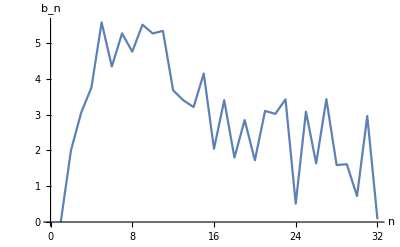

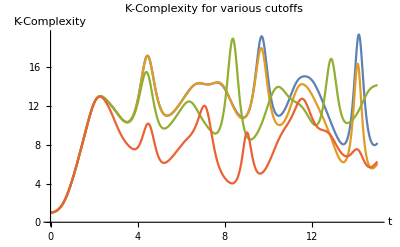

```mathematica
H=IsingSum[3,PauliMatrix[3],2,PauliMatrix[3],PauliMatrix[1]];
Op=IsingSum[3,0,2,PauliMatrix[3],0];
nmax=40;
prec=40;
btol=10^(-6);
tmax=15;

(*Calculate and Plot Lanczos coefficients*)
Timing[b=LanczosNum[H,Op,nmax,prec,btol];] (*Outputs time taken to calculate the Lanczos coefficients in seconds*)
bmax =Length[b]-1; (*Number of non-zero Lanczos coefficients*)
ListLinePlot[b,AxesLabel->{"n","b_n"}]

(*Calculate and Plot K-Complexity*)
K=KComplexityFromBs[b,bmax,tmax];
K2=KComplexityFromBs[b,bmax-5,tmax];
K3=KComplexityFromBs[b,bmax-10,tmax];
K4=KComplexityFromBs[b,bmax-15,tmax];
Plot[{K,K2,K3,K4},{t,0,tmax},PlotRange->{Full,{0,Automatic}},AxesLabel->{"t","K-Complexity"}, PlotLabel->"K-Complexity for various cutoffs"]
```

## Local vs non-local operators

Now we can find the K-complexity for various operators and compare. 
Below we have the Hamiltonian for a Ising chain of length 4 with a transverse and longitudinal magnetic field.
	H = 	-J(σ_z  ⊗ σ_z ⊗ Id ⊗ Id) +  (Id ⊗ σ_z ⊗ σ_z ⊗ Id) + (Id ⊗ Id ⊗ σ_z ⊗ σ_z)
		+B1 (σ_z  ⊗ Id ⊗ Id ⊗ Id) +  (Id⊗ σ_z  ⊗ Id ⊗ Id)+ (Id ⊗ Id ⊗ σ_z  ⊗ Id) + (Id  ⊗ Id ⊗ Id ⊗ σ_z)
		+B2 (σ_x  ⊗ Id ⊗ Id ⊗ Id) +  (Id⊗ σ_x  ⊗ Id ⊗ Id)+ (Id ⊗ Id ⊗ σ_x  ⊗ Id) + (Id  ⊗ Id ⊗ Id ⊗ σ_x)
where we (for now) set J=B1=B2=1.
We will use the operators 
	Op1 =  (σ_z  ⊗ Id ⊗ Id ⊗ Id) +  (Id⊗ σ_z  ⊗ Id ⊗ Id)+ (Id ⊗ Id ⊗ σ_z  ⊗ Id) + (Id  ⊗ Id ⊗ Id ⊗ σ_z) 
	Op2 =  (σ_z  ⊗ σ_z ⊗ Id ⊗ Id) +  (Id ⊗ σ_z ⊗ σ_z ⊗ Id) + (Id ⊗ Id ⊗ σ_z ⊗ σ_z)
	Op3 =  (σ_z  ⊗ σ_z ⊗ σ_z ⊗ Id)+ (Id ⊗ σ_z  ⊗ σ_z ⊗ σ_z)

```mathematica
H=IsingSum[5,PauliMatrix[3],2,PauliMatrix[3],PauliMatrix[1]];
nmax=200;
prec=200;
tmax=10;
(*Opx has is on x sites*)
Op1=IsingSum[5,0,2,PauliMatrix[3],0];
Op2=IsingSum[5,PauliMatrix[3],2,0,0];
Op3=IsingSum[5,PauliMatrix[3],3,0,0];

(*Calculate and Plot Lanczos coefficients*)
b1=LanczosNum[H,Op1,nmax,prec,10^(-6)];
b2=LanczosNum[H,Op2,nmax,prec,10^(-6)];
b3=LanczosNum[H,Op3,nmax,prec,10^(-6)];
ListLinePlot[{b1,b2,b3},AxesLabel->{"n","b_n"},PlotLabels->{"1-site","2-site","3-site"}]

(*Calculate and Plot K-Complexity*)
K1 = KComplexityFromBs[b1,Length[b1]-1,tmax];
K2 = KComplexityFromBs[b2,Length[b2]-1,tmax];
K3 = KComplexityFromBs[b3,Length[b3]-1,tmax];
Plot[{K1,K2,K3},{t,0,tmax},PlotRange->{Full,{0,Automatic}},AxesLabel->{"t","K-Complexity"}, PlotLabels->{"1-site","2-site","3-site"}]
```

-Graphics-

-Graphics-

## Investigating Integrability using K-Complexity

10.1103./PhysRevE.107.024217 by Espanol and Wisniacki they investigate Krylov complexity as a measure of Chaos.
It is conjectured that the long-term saturation of a system is dependent on the amount of chaos in the system. In order to study this they study the complexity of various operators during the transition of a system from integrability to chaos.

### Diagnostics of Chaos

1. Spectral Characterization
We can quantify the chaoticity of the system using a spectral measure η .  Given a Hamiltonian in a symmetry subspace, we can order the energy levels E_n . The nearest neighbour spacing between energy levels will be s_n= e_(n+1)-e_n .  The ratio of consecutive spacings will be r_n=s_n/(s_(n-1)) . We then define an indicator R_n=min(r_n, 1/r_n) - this ensures the ratio is always < 1. The average value of the Indicator, R, is minimum if the distribution of the spacings, s_n, is Poissonian (R_p) and maximum if it is Wigner-Dyson distributed (R_WD ). So we can thus construct a normalized measure (η) such that we can identify the system as integrable when η ~ 0 and chaotic if η ~ 1 :
	 η  =  (R_avg  -  R_p)/(R_WD  -  R_p) 

2. Dispersion of Lanczos coefficients
We can use a measure of dispersion  of the standard deviation of the logarithmic difference between successive Lanczos coefficients:
	σ_log= SD[log(b_n/(b_(n-1)))]

3. Krylov Complexity :)

### Spectral Characterization

```mathematica
H=IsingSum[3,PauliMatrix[3],2,PauliMatrix[3],PauliMatrix[1]];
En = N[Eigenvalues[H],15];
S=Table[En[[n+1]]-En[[n]],{n,1,Length[En]-1}];
ratio = Table[S[[n+1]]/S[[n]],{n,1, Length[S]-1}];
R = Table[rn=ratio[[n]];
If[rn<1/rn,rn,1/rn] ,{n,1,Length[ratio]}];
```

### Dispersion of Lanczos Coefficients

```mathematica
LogDispersion[b_] :=
Module[{logb},logb = Table[Log[b[[n]]/b[[n-1]]],{n,2,Length[b]}];
N[StandardDeviation[logb],20]]
```

### K-Complexity of the Ising Model in Integrable and chaotic regimes

The Ising model with transverse and longitudinal magnetic field has the Hamiltonian:
	H = -J ∑_k (σ^z)_k(σ^z)_(k+1)  + ∑_k h_x(σ^x)_k+h_z(σ^z)_k
This model is integrable in the limit of h_x>>h_z and h_x<<h_z , but it exhibits chaos when h_x and h_z  are of comparable strength.

```mathematica
HIntegrable=IsingSum[3,PauliMatrix[3],2,PauliMatrix[3],100*PauliMatrix[1]];
HChaos=IsingSum[3,PauliMatrix[3],2,PauliMatrix[3],PauliMatrix[1]];
Op=IsingSum[3,0,2,PauliMatrix[3],0];
nmax=40;
prec=40;
tmax=100;
btol=10^(-3);
(*Calculate and Plot Lanczos coefficients*)
bIntegrable=LanczosNum[HIntegrable,Op,nmax,prec,btol];
bChaos = LanczosNum[HChaos,Op,nmax,prec,btol];
ListLinePlot[{bIntegrable, bChaos},AxesLabel->{"n","b_n"},PlotLabels->{"Integrable", "Chaotic"}]

(*Calculate and Plot K-Complexity*)
KIntegrable=NormKComplexityFromBs[bIntegrable,Length[bIntegrable]-1,tmax];
KChaos=NormKComplexityFromBs[bChaos,Length[bIntegrable]-1,tmax];
Plot[{KIntegrable, KChaos},{t,0,tmax},PlotRange->{Full,{0,Automatic}},AxesLabel->{"t","K-Complexity"}, PlotLabels->{"Integrable", "Chaotic"}]
```

Cut-off reached at n= 32, since b_n and btol are 0.0002 and 1/1000

Cut-off reached at n= 34, since b_n and btol are 0. and 1/1000

-Graphics-

-Graphics-

## Analysing the loss of accuracy in the early-time K-Complexity as the Lanczos coefficient list is truncated

We will use a Hamiltonian with the maximum chain length L that my computer can find all the Lanczos coefficients for. Right now that is L=5
We will use a 2-site operator. Op2 =  (σ_z  ⊗ σ_x ⊗ Id ⊗ Id)
We can then take a range of cut-offs of the Lanczos coefficients. Say {5%, 10%, 50%, 100%} of the total Lanczos coefficients for L=5 (which is here ~512).
For each of these Lanczos coefficient sets, we can calculate the early-time K-complexity (up to say t=2)

Cut-off reached at n= 34, since tolval(b/(Norm[H, O]))) and btol are 0. and 1/1000000

{0.0625,Null}

-Graphics-

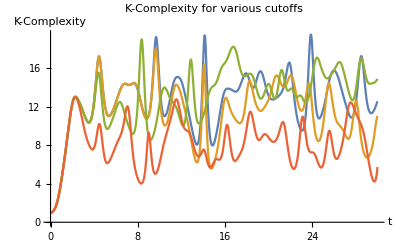

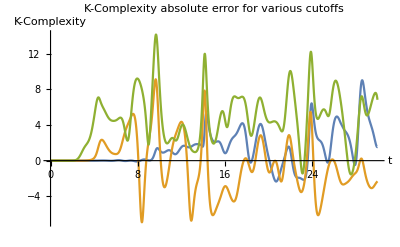

```mathematica
H=IsingSum[3,PauliMatrix[3],2,PauliMatrix[3],PauliMatrix[1]];
Op=IsingSum[3,0,2,PauliMatrix[3],0];
nmax=40;
prec=45;
btol=10^(-6);
tmax=30;

(*Calculate and Plot Lanczos coefficients*)
Timing[b=LanczosNum[H,Op,nmax,prec,btol];] (*Outputs time taken to calculate the Lanczos coefficients in seconds*)
bmax =Length[b]-1; (*Number of non-zero Lanczos coefficients*)
ListLinePlot[b,AxesLabel->{"n","b_n"}]

(*Calculate and Plot K-Complexity*)
KAll=KComplexityFromBs[b,bmax,tmax];
K2=KComplexityFromBs[b,bmax-5,tmax];
K3=KComplexityFromBs[b,bmax-10,tmax];
K4=KComplexityFromBs[b,bmax-15,tmax];
Plot[{KAll,K2,K3,K4},{t,0,tmax},PlotRange->{Full,{0,Automatic}},AxesLabel->{"t","K-Complexity"}, PlotLabel->"K-Complexity for various cutoffs"]
Plot[{KAll-K2,KAll-K3,KAll-K4},{t,0,tmax},AxesLabel->{"t","K-Complexity"}, PlotLabel->"K-Complexity absolute error for various cutoffs"]
```

Lets try to find the time after which the absolute error of the K(t) is greater than a tolerance, say 2%.

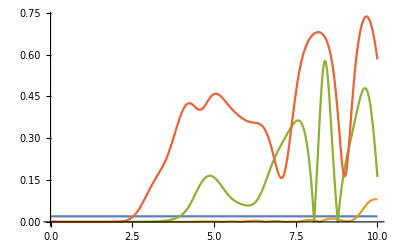

```mathematica
ErrTol=2/100;
RelErr2=Abs[(KAll-K2)/KAll];
RelErr3=Abs[(KAll-K3)/KAll];
RelErr4=Abs[(KAll-K4)/KAll];
Plot[{ErrTol,RelErr2,RelErr3, RelErr4},{t,0,tmax}, PlotRange->{0,Automatic}]
```